## Packages import and definitions

```mathematica
SetDirectory[NotebookDirectory[]];
Get["../Mathematica_packages/"<>#]&/@{"Chaometer.wl","QMB.wl"};
```

```mathematica
(* Canal completamente depolarizante que actúa sobre el primer espín de una cadena de N espines *)
DepolarizingChannel[ρ_,L_]:=
Module[{kraus},
(* Construir operadores de Kraus *)
kraus=KroneckerProduct[#,IdentityMatrix[2^(L-1)]]&/@ArrayReshape[IdentityMatrix[4]/√2,{4,2,2}];

(* Aplicar canal en su forma de Kraus a ρ *)
Total[#.ρ.ConjugateTranspose[#]&/@kraus]
]
```

```mathematica
(* Evolución de la matriz de densidad *)
DensityMatrixEvolution[ρ_,U_]:=U.ρ.ConjugateTranspose[U]
```

### Parameters setup

```mathematica
L=11(*number of spins*);
{hx,hz,J}={1.,0.5,ConstantArray[1.,L-1]}(*hz=0.5 chaotic, hz=2.5 regular*)
```

{1.,0.5,{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}

```mathematica
Module[{H},
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenvalsH,eigenvecsH}=N[Chop[Eigensystem[H]]];
]
```

```mathematica
(*Three initial random states of the environment Subscript[ψ, 0E]=Subscript[random, 1]⊗…⊗Subscript[random, L-1]*)
SeedRandom[32371];
ψ0E=Table[RandomChainProductState[L-1],3];
```

```mathematica
superoperators=ToExpression[Import["/home/jadeleon/Documents/quantum_chaotic_channels/ja_files/chaotic/superoperators_2.csv"][[2;;]](*la primera fila tiene la info*)];
```

```mathematica
(* Check de que un superoperador random sea el correcto comparando con la construccion de alguno  *)
t=RandomChoice[Range[0,50,0.1]](* un tiempo aleatorio *);
MatrixForm[Round[#,10.^-7]]&/@{Chop@Superoperator[t,ψ0E[[2]](*número de estado aleatorio*),eigenvalsH,eigenvecsH,L],superoperators[[t/0.1+1]]}
Equal@@%
```

{(0.493083 | 0.0122412+0.0119287 ⅈ | 0.0122412-0.0119287 ⅈ | 0.475635
0.0182229+0.0081882 ⅈ | 0.0410292-0.006847 ⅈ | 0.0367151+0.0005877 ⅈ | -0.0344784+0.0009147 ⅈ
0.0182229-0.0081882 ⅈ | 0.0367151-0.0005877 ⅈ | 0.0410292+0.006847 ⅈ | -0.0344784-0.0009147 ⅈ
0.506917 | -0.0122412-0.0119287 ⅈ | -0.0122412+0.0119287 ⅈ | 0.524365),(0.493083 | 0.0122412+0.0119287 ⅈ | 0.0122412-0.0119287 ⅈ | 0.475635
0.0182229+0.0081882 ⅈ | 0.0410292-0.006847 ⅈ | 0.0367151+0.0005877 ⅈ | -0.0344784+0.0009147 ⅈ
0.0182229-0.0081882 ⅈ | 0.0367151-0.0005877 ⅈ | 0.0410292+0.006847 ⅈ | -0.0344784-0.0009147 ⅈ
0.506917 | -0.0122412-0.0119287 ⅈ | -0.0122412+0.0119287 ⅈ | 0.524365)}

True

```mathematica
chois=1/2*Reshuffle/@superoperators;
```

```mathematica
choiPurities=Transpose[{Range[0,50,0.1],Chop[Purity/@chois]}];
```

## COE

```mathematica
L=3;(* number of spins *)
```

```mathematica
SeedRandom[2312];
ψ=RandomChainProductState[L-1];
U=RandomVariate[CircularOrthogonalMatrixDistribution[2^L]];
```

```mathematica
U=Dot@@Table[U,10]
```

{{-0.171588-0.123556 ⅈ,0.112502-0.144908 ⅈ,0.139943-0.170746 ⅈ,0.145717-0.422729 ⅈ,0.00756406+0.0289037 ⅈ,-0.344643-0.10008 ⅈ,0.672847+0.0281361 ⅈ,0.296034-0.046111 ⅈ},{0.112502-0.144908 ⅈ,-0.611907+0.131792 ⅈ,-0.161034+0.149133 ⅈ,0.216715-0.326946 ⅈ,0.131308-0.363708 ⅈ,-0.286981+0.206095 ⅈ,-0.120824+0.0250478 ⅈ,-0.0249667+0.286891 ⅈ},{0.139943-0.170746 ⅈ,-0.161034+0.149133 ⅈ,-0.72467+0.194993 ⅈ,-0.103888+0.0671267 ⅈ,-0.0261335+0.205134 ⅈ,0.0339563-0.286062 ⅈ,0.158497+0.107974 ⅈ,0.249862-0.315695 ⅈ},{0.145717-0.422729 ⅈ,0.216715-0.326946 ⅈ,-0.103888+0.0671267 ⅈ,0.176475-0.401464 ⅈ,0.0345809+0.0803373 ⅈ,0.35229+0.40783 ⅈ,-0.102717+0.146208 ⅈ,-0.189798-0.269365 ⅈ},{0.00756406+0.0289037 ⅈ,0.131308-0.363708 ⅈ,-0.0261335+0.205134 ⅈ,0.0345809+0.0803373 ⅈ,-0.285344-0.748391 ⅈ,0.0669986-0.204666 ⅈ,-0.0697502-0.0858126 ⅈ,0.241258-0.20211 ⅈ},{-0.344643-0.10008 ⅈ,-0.286981+0.206095 ⅈ,0.0339563-0.286062 ⅈ,0.35229+0.40783 ⅈ,0.0669986-0.204666 ⅈ,0.238874+0.222945 ⅈ,0.262184+0.0706498 ⅈ,-0.092326-0.370886 ⅈ},{0.672847+0.0281361 ⅈ,-0.120824+0.0250478 ⅈ,0.158497+0.107974 ⅈ,-0.102717+0.146208 ⅈ,-0.0697502-0.0858126 ⅈ,0.262184+0.0706498 ⅈ,0.554074-0.147991 ⅈ,-0.180155+0.123437 ⅈ},{0.296034-0.046111 ⅈ,-0.0249667+0.286891 ⅈ,0.249862-0.315695 ⅈ,-0.189798-0.269365 ⅈ,0.241258-0.20211 ⅈ,-0.092326-0.370886 ⅈ,-0.180155+0.123437 ⅈ,-0.185341-0.479014 ⅈ}}

```mathematica
1/2*Chop[Braket[ψ,MatrixPartialTrace[DensityMatrixEvolution[DepolarizingChannel[DensityMatrixEvolution[KroneckerProduct[IdentityMatrix[2]/2,Dyad[ψ]],U],L],ConjugateTranspose[U]],1,{2,4}].ψ]]
```

0.20319

```mathematica
UU[H_,t_]:=MatrixExp[-ⅈ H t]
```

### Varying algo

```mathematica
choiPurities={};
```

```mathematica
L=3;(* number of spins *)
SeedRandom[2314];
ψ=RandomChainProductState[L-1];
U=RandomVariate[CircularOrthogonalMatrixDistribution[2^L]];
SeedRandom[2312];
H=RandomVariate[GaussianOrthogonalMatrixDistribution[2^L]];
choiPurity=Table[
U=UU[H,t];
Chop[Braket[ψ,MatrixPartialTrace[DensityMatrixEvolution[DepolarizingChannel[DensityMatrixEvolution[KroneckerProduct[IdentityMatrix[2]/2,Dyad[ψ]],U],L],ConjugateTranspose[U]],1,{2,2^(L-1)}].ψ]]
,{t,0,25,0.1}];
```

```mathematica
Mean[choiPurity]
```

0.46371

```mathematica
Mean[choiPurity]
```

0.458181

```mathematica
data
```

{{3,0.444663},{4,0.351698},{5,0.300509},{6,0.27837},{7,0.265072},{8,0.258977},{9,0.255951}}

```mathematica
AppendTo[choiPurities,Transpose[{Range[0,25,0.1],choiPurity}]];
```

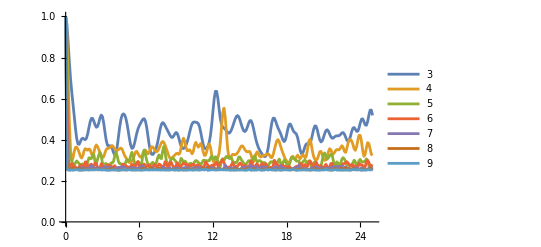

```mathematica
ListPlot[choiPurities,Joined->True,PlotRange->{All,{0,1}},PlotLegends->Range[3,9]]
```

```mathematica
Export["figs/choi_purity_goe_L_3_to_9.pdf",%]
```

figs/choi_purity_goe_L_3_to_9.pdf

{a→0.26577,b→1.32096,c→1.}

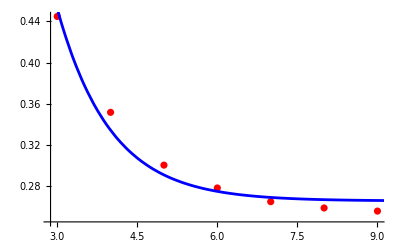

```mathematica
(*Sample data:a list of (x,y) pairs*)data=Transpose[{Range[3,9],Mean/@choiPurities[[All,All,2]]}];

(*Nonlinear model fitting*)
fit=NonlinearModelFit[data,a+Exp[-x+b],{a,b,c},x];

(*Parameters obtained from the fit*)
parameters=fit["BestFitParameters"]

(*Plot the data points and the fitted curve*)
Show[ListPlot[data,PlotStyle->Red],Plot[fit[x],{x,0,10},PlotStyle->Blue]]
```

```mathematica
Export["figs/choi_purity_goe_asymptotic_vs_L.pdf",%]
```

figs/choi_purity_goe_asymptotic_vs_L.pdf